```mathematica
ClearAll["Global`*"]
Needs["NDSolve`FEM`"]
```

wood

WolframAlphaQueryResults

```mathematica
BeamLength= 5; (* beam length *)
BeamWidth = 1/10;  (* beam width *)
LoadDensity[X_]:=q; (* load density as a function of X *)

q:=61.8; 
EE:= 9400000; (* Young's modulus *) 
Izz:= 3;(* Moment of inertia. *)
```

```mathematica
EulerBernoulliSolution = 
DSolve[
{
D[EE*Izz*D[y[X], X, X], X, X] == LoadDensity[X], 
y[-BeamLength/2]==0, 
y[BeamLength/2]==0, 
y'[-BeamLength/2]==0, 
y'[BeamLength/2]==0
}, 
y, 
X] (* Euler--Bernoulli beam theory, fixed ends, perpendicular to the wall. *)
```

{{y→Function[{X},3.56688×10^-6+2.11758×10^-22 X-1.1414×10^-6 X^2-4.51751×10^-23 X^3+9.13121×10^-8 X^4]}}

```mathematica
DisplacementEulerBernoulli[X_, Y_]:= {-Y*Sin[ArcTan[y'[X]]],y[X] + Y*(Cos[ArcTan[y'[X]]]-1)  }  /. EulerBernoulliSolution(* Displacement reconstruction from the solution to the Euler--Bernoulli equation. *)
```

```mathematica
DisplacementEulerBernoulli[X, Y]
```

{{-((2.11758×10^-22-2.2828×10^-6 X-1.35525×10^-22 X^2+3.65248×10^-7 X^3) Y)/(√(1+(2.11758×10^-22-2.2828×10^-6 X-1.35525×10^-22 X^2+3.65248×10^-7 X^3)^2)),3.56688×10^-6+2.11758×10^-22 X-1.1414×10^-6 X^2-4.51751×10^-23 X^3+9.13121×10^-8 X^4+(-1+1/(√(1+(2.11758×10^-22-2.2828×10^-6 X-1.35525×10^-22 X^2+3.65248×10^-7 X^3)^2))) Y}}

```mathematica
u=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[1]]]; (* horizontal displacement *)
v=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[2]]]; (* vertical displacement *)

u[X,Y]
v[X,Y]
```

-((2.11758×10^-22-2.2828×10^-6 X-1.35525×10^-22 X^2+3.65248×10^-7 X^3) Y)/(√(1+(2.11758×10^-22-2.2828×10^-6 X-1.35525×10^-22 X^2+3.65248×10^-7 X^3)^2))

3.56688×10^-6+2.11758×10^-22 X-1.1414×10^-6 X^2-4.51751×10^-23 X^3+9.13121×10^-8 X^4+(-1+1/(√(1+(2.11758×10^-22-2.2828×10^-6 X-1.35525×10^-22 X^2+3.65248×10^-7 X^3)^2))) Y

```mathematica
BeamMesh = ToElementMesh[Rectangle[{-BeamLength/2, -BeamWidth/2}, {BeamLength/2, BeamWidth/2}]]; (* generate mesh, default setting for number of elements *)
```

```mathematica
uif=ElementMeshInterpolation[{BeamMesh},u@@@BeamMesh["Coordinates"]]; (* generate interpolation functions using the given mesh *)
vif=ElementMeshInterpolation[{BeamMesh},v@@@BeamMesh["Coordinates"]]; (* generate interpolation functions using the given mesh *)
```

```mathematica
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]; (* deform the generated mesh with the given displacement function *)
```

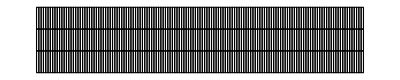

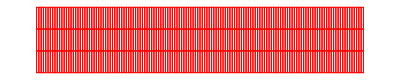

```mathematica
Show[BeamMesh["Wireframe"], ImageSize->Full]
Show[BeamMeshDeformed, ImageSize->Full]
```

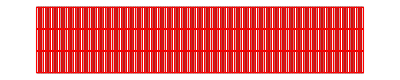

```mathematica
Show[{BeamMesh["Wireframe"],BeamMeshDeformed}, ImageSize->Full]
```

```mathematica
ImageReflect[%] (* The convention in beam theory is that the positive y-axis is pointing downwards, hence we need to flip the figure. *)
```

-Graphics-

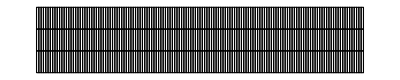

```mathematica
Show[
BeamMesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[GrayLevel[0.9]],FaceForm[]]]],
ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Black],FaceForm[]]]],
ImageSize->Full
] (* Black and white visualisation of the same. *)
```

```mathematica
ImageReflect[%]
```

-Graphics-